# Checking parallel and perpendicular components

Hi Ben, I’m just checking that eqs (4) and (5) in the paper are correct - these correspond to the parallel and perpendicular components of the field. I start by writing out the classical RF field:

```mathematica
ex = {1,0,0};
ey = {0,1,0};
ez = {0,0,1};
Brf =B Cos[ω t]ex - κ B Sin[ω t] ey
```

{B Cos[t ω],-B κ Sin[t ω],0}

## Defining the transformation between frames

Now transform the field in the lab frame to the local coordinate system.We first rotate through the y-axis by an angle θ, then rotate through the x-axis by angle ϕ. Note that this is different to what was in the original text of the Appendix, but the rotation matrix I get is the same as yours, so I think the text must have been wrong there? This text is not present in the current version of the paper.

```mathematica
R1 = RotationMatrix[-θ, ey];
(* R2 = FullSimplify[RotationMatrix[γ, R1.ex], Assumptions->{θ ∈ Reals}]; *)
R2 =  RotationMatrix[ϕ, ex]
transformM = R2.R1;
Row[{"R1=",MatrixForm[R1], ", R2=", MatrixForm[R2]}]
Row[{"Rotation Matrix=",MatrixForm[transformM]}]
BrfLocal = transformM.Brf;
Row[{"B field in local coordinates=", MatrixForm[BrfLocal]}]
Row[{"In frame X': e_x=", MatrixForm[transformM.ex],", e_y=", MatrixForm[transformM.ey],", e_z=", MatrixForm[transformM.ez]}]
Row[{"In frame X: e_x'=", MatrixForm[FullSimplify[Inverse[transformM].ex]],", e_y'=", MatrixForm[FullSimplify[Inverse[transformM].ey]],", e_z'=", MatrixForm[FullSimplify[Inverse[transformM].ez]]}]
```

{{1,0,0},{0,Cos[ϕ],-Sin[ϕ]},{0,Sin[ϕ],Cos[ϕ]}}

R1=(Cos[θ] | 0 | -Sin[θ]
0 | 1 | 0
Sin[θ] | 0 | Cos[θ]), R2=(1 | 0 | 0
0 | Cos[ϕ] | -Sin[ϕ]
0 | Sin[ϕ] | Cos[ϕ])

Rotation Matrix=(Cos[θ] | 0 | -Sin[θ]
-Sin[θ] Sin[ϕ] | Cos[ϕ] | -Cos[θ] Sin[ϕ]
Cos[ϕ] Sin[θ] | Sin[ϕ] | Cos[θ] Cos[ϕ])

B field in local coordinates=(B Cos[θ] Cos[t ω]
-B Cos[t ω] Sin[θ] Sin[ϕ]-B κ Cos[ϕ] Sin[t ω]
B Cos[ϕ] Cos[t ω] Sin[θ]-B κ Sin[ϕ] Sin[t ω])

In frame X': e_x=(Cos[θ]
-Sin[θ] Sin[ϕ]
Cos[ϕ] Sin[θ]), e_y=(0
Cos[ϕ]
Sin[ϕ]), e_z=(-Sin[θ]
-Cos[θ] Sin[ϕ]
Cos[θ] Cos[ϕ])

In frame X: e_x'=(Cos[θ]
0
-Sin[θ]), e_y'=(-Sin[θ] Sin[ϕ]
Cos[ϕ]
-Cos[θ] Sin[ϕ]), e_z'=(Cos[ϕ] Sin[θ]
Sin[ϕ]
Cos[θ] Cos[ϕ])

### Check the quantisation axis is correct

Let's check that the transformation uses the same definition of θ and ϕ as in the paper. It should follow that applying the inverse transformation to e_z will give us a vector equal to the quantisation axis in the lab frame.

We define the quadrupole field, and then a vector corresponding to the quantisation axis. We apply the inverse of the transformation matrix, to map the quantisation axis (z axis) in the transformed frame back to the lab frame. This vector should be the same as the quantisation axis vector in the lab frame.

```mathematica
BQuadField = {BQuad x, BQuad y, - 2 BQuad z};
QuantisationAxisVector = FullSimplify[BQuadField / Norm[BQuadField], Assumptions -> {Bquad ∈ Reals, x∈ Reals, y ∈ Reals, z ∈ Reals, BQuad > 0}]
ThetaDefinition = θ -> ArcCos[-2 z / (x^2+4 z^2)^(1/2)];
PhiDefinition = ϕ-> ArcCos[(x^2+4 z^2)^(1/2) / (x^2+y^2+4 z^2)^(1/2)];
FullSimplify[Inverse[transformM].ez/.{ThetaDefinition, PhiDefinition}, Assumptions->{x>0, y>0, z>0, x∈Reals, y∈Reals, z∈Reals}]
```

{x/(√(x^2+y^2+4 z^2)),y/(√(x^2+y^2+4 z^2)),-(2 z)/(√(x^2+y^2+4 z^2))}

{x/(√(x^2+y^2+4 z^2)),y/(√(x^2+y^2+4 z^2)),-(2 z)/(√(x^2+y^2+4 z^2))}

## Determining the interaction

Calculate the value of Β dot μ in the local frame. We rewrite the operators F_x and F_y in terms of the raising and lowering operators.

```mathematica
Fx = (Fp + Fm)/2;
Fy = (Fp - Fm)/(2 ⅈ);
Fvec = {Fx, Fy, Fz};
FdotB = gF uB Dot[Fvec, BrfLocal]
```

gF uB (1/2 B (Fm+Fp) Cos[θ] Cos[t ω]-1/2 ⅈ (-Fm+Fp) (-B Cos[t ω] Sin[θ] Sin[ϕ]-B κ Cos[ϕ] Sin[t ω])+Fz (B Cos[ϕ] Cos[t ω] Sin[θ]-B κ Sin[ϕ] Sin[t ω]))

## Extract α and β as coefficients of Exp[ⅈ ω t]

Take the coefficient of Exp[i ω t], as per the definition of α and β according to eq (6). From this it follows that the coefficient in front of F_- should correspond to α, the coefficient in front of F_+ to β.

```mathematica
cFz = FullSimplify[ExpToTrig[Coefficient[Coefficient[TrigToExp[Dot[Fvec, BrfLocal]],Exp[ⅈ ω t]],Fz]]];
Row[{"ζ = ", cFz}]
cFm = FullSimplify[ExpToTrig[Coefficient[Coefficient[TrigToExp[Dot[Fvec, BrfLocal]],Exp[ⅈ ω t]],Fm]]];
Row[{"α = ", cFm}]
cFp = FullSimplify[ExpToTrig[Coefficient[Coefficient[TrigToExp[Dot[Fvec, BrfLocal]],Exp[ⅈ ω t]],Fp]]];
Row[{"β = ", cFp}]
```

ζ = 1/2 B (Cos[ϕ] Sin[θ]+ⅈ κ Sin[ϕ])

α = 1/4 B (Cos[θ]-κ Cos[ϕ]-ⅈ Sin[θ] Sin[ϕ])

β = 1/4 B (Cos[θ]+κ Cos[ϕ]+ⅈ Sin[θ] Sin[ϕ])

### Test : Do we get correct coherence terms?

Take the bottom of the shell, circular polarised

```mathematica
circBottomOfShell = {ϕ-> 0, θ-> 0, κ-> 1};
```

In this limit we get definitions of α, β of

```mathematica
αDef = cFm/.circBottomOfShell
βDef = cFp/.circBottomOfShell
ζDef = cFz/.circBottomOfShell
```

0

B/2

0

Check to see if this gives coherence terms that are correct. We use the basis m_F={-1,0,1}. The Sqrt[2] comes from the Clebsch-Gordon factors for an F=1 system.

```mathematica
FzMatrix = {{-1,0,0}, {0,0,0}, {0,0,1}};
Row[{"F_z=", MatrixForm[FzMatrix]}]
FpMatrix = {{0, 1, 0},{0, 0, 1}, {0,0,0}} Sqrt[2];
Row[{"F_-=", MatrixForm[FpMatrix]}]
FmMatrix = {{0, 0, 0},{1, 0, 0}, {0,1,0}} Sqrt[2];
Row[{"F_+=", MatrixForm[FmMatrix]}]
Hint = μ(αDef FmMatrix+βDef FpMatrix + ζDef FzMatrix) Exp[ⅈ ω t] + μ(Conjugate@αDef FpMatrix+Conjugate@βDef FmMatrix+ Conjugate@ζDef FzMatrix) Exp[-ⅈ ω t];
Hint = FullSimplify[Hint, Assumptions->{B∈Reals}];
Hatom = FzMatrix ω0;
Row[{"H_int=", MatrixForm[Hint], "; H=", MatrixForm[Hatom + Hint]}]
```

F_z=(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

F_-=(0 | √2 | 0
0 | 0 | √2
0 | 0 | 0)

F_+=(0 | 0 | 0
√2 | 0 | 0
0 | √2 | 0)

H_int=(0 | (B ⅇ^(ⅈ t ω) μ)/(√2) | 0
(B ⅇ^(-ⅈ t ω) μ)/(√2) | 0 | (B ⅇ^(ⅈ t ω) μ)/(√2)
0 | (B ⅇ^(-ⅈ t ω) μ)/(√2) | 0); H=(-ω0 | (B ⅇ^(ⅈ t ω) μ)/(√2) | 0
(B ⅇ^(-ⅈ t ω) μ)/(√2) | 0 | (B ⅇ^(ⅈ t ω) μ)/(√2)
0 | (B ⅇ^(-ⅈ t ω) μ)/(√2) | ω0)

Transform into rotating frame, take rotating wave approximation and solve for eigenvalues.

```mathematica
trans = DiagonalMatrix[Exp[ⅈ ω0 Diagonal[FzMatrix]t]];
Row[{"Interaction picture: ",  MatrixForm[trans.(Hatom+Hint).Inverse[trans]]}]
trans = DiagonalMatrix[Exp[ⅈ ω Diagonal[FzMatrix]t]];
Row[{"Transformation matrix to rotating frame: ",  MatrixForm[trans]}]
Hrot = FullSimplify[trans.(Hatom+Hint).Inverse[trans], Assumptions->{t ∈Reals, ω ∈ Reals}];
Row[{"Hamiltonian in Rotating wave approximation, H_rot=", MatrixForm[Hrot]}]
```

Interaction picture: (-ω0 | (B ⅇ^(ⅈ t ω-ⅈ t ω0) μ)/(√2) | 0
(B ⅇ^(-ⅈ t ω+ⅈ t ω0) μ)/(√2) | 0 | (B ⅇ^(ⅈ t ω-ⅈ t ω0) μ)/(√2)
0 | (B ⅇ^(-ⅈ t ω+ⅈ t ω0) μ)/(√2) | ω0)

Transformation matrix to rotating frame: (ⅇ^(-ⅈ t ω) | 0 | 0
0 | 1 | 0
0 | 0 | ⅇ^(ⅈ t ω))

Hamiltonian in Rotating wave approximation, H_rot=(-ω0 | (B μ)/(√2) | 0
(B μ)/(√2) | 0 | (B μ)/(√2)
0 | (B μ)/(√2) | ω0)

Last, but by no means least, extract the eigenvalues of the rotating wave approximation. For fun, we also plot the eigenvectors in the rotating frame.

```mathematica
Eigenvalues[Hrot]
```

{0,-√(B^2 μ^2+ω0^2),√(B^2 μ^2+ω0^2)}

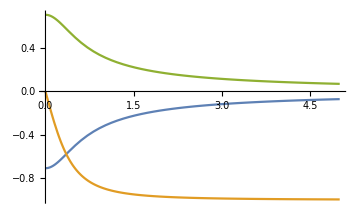
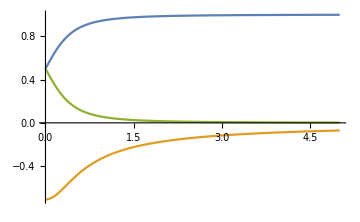
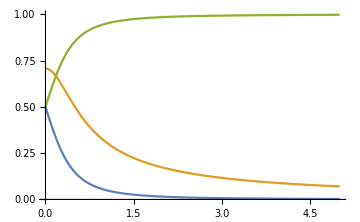
-Graphics-Size-Graphics-Size-Graphics-

```mathematica
eigenV = Eigenvectors[Hrot] /Map[Norm,Eigenvectors[Hrot]];
ACrule = { μ-> 1, B -> 0.5};
Row[Map[Function[x,Plot[x, {ω0,0, 5}, ImageSize-> Medium]], eigenV/.ACrule], Size]
```

Note that by making the rotating wave approximation we have transformed into the interaction picture with rotating basis vectors:

```mathematica
Row[Map[Function[x,MatrixForm[Inverse[trans].x]], {{1,0,0},{0,1,0},{0,0,1}}]]
```

(ⅇ^(ⅈ t ω)
0
0)(0
1
0)(0
0
ⅇ^(-ⅈ t ω))